```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"]
```

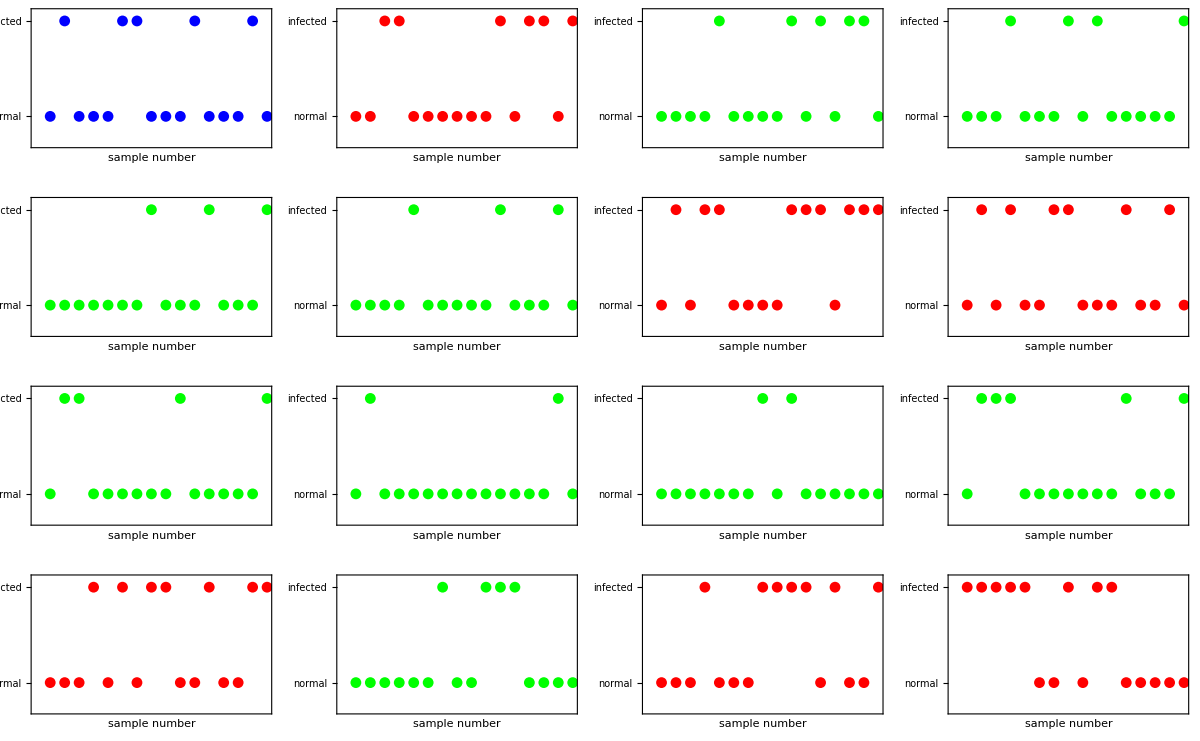

```mathematica
data = {{0,1,0,0},{0,1,1,0},{0,0,1,0},{0,0,1,0}};
yTicks = {{0,"normal"},{1,"infected"}};
xTicks = Table[{i-1,i},{i,1,16,1}];
fPlot[data_]:=ListPlot[Flatten@data,Frame->{True,True,False,False},FrameTicks->{None,yTicks},FrameLabel->{"sample number",},PlotStyle->Blue,BaseStyle->{FontSize->12},PlotRange->{Full,{-0.3,1.1}},Axes->{False,False}]
fPlotDataFake[dataReal_]:=Module[{dataFake = RandomVariate[BernoulliDistribution[(Total@Flatten@dataReal)/16],{16}],aColour},aColour = If[(Total@dataFake)>Total@Flatten@dataReal,Red,Green]; ListPlot[Flatten@dataFake,Frame->{True,True,False,False},FrameTicks->{None,yTicks},FrameLabel->{"sample number",},PlotStyle->aColour,BaseStyle->{FontSize->12},PlotRange->{Full,{-0.3,1.1}},Axes->{False,False}]]
gFinal=Show[GraphicsGrid[{{fPlot@data,fPlotDataFake@data,fPlotDataFake@data,fPlotDataFake@data},{fPlotDataFake@data,fPlotDataFake@data,fPlotDataFake@data,fPlotDataFake@data},{fPlotDataFake@data,fPlotDataFake@data,fPlotDataFake@data,fPlotDataFake@data},{fPlotDataFake@data,fPlotDataFake@data,fPlotDataFake@data,fPlotDataFake@data}}],ImageSize->1200]
```

```mathematica
Export["Evaluation_bacteriaPPC.pdf",gFinal]
```

Evaluation_bacteriaPPC.pdf